## A reanalysis of the SH0ES data for H_0. Reanalysis of Individual Cepheid m_H^W slope data. Homogeneity of the Cepheid modeling parameter Z_W.

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",General::luc,NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,FindRoot::lstol,ListInterpolation::inhr,FindMinimum::lstol];
```

## Matrix of Measurements Y - Data - Error Matrix C

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
```

```mathematica
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
```

```mathematica
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
```

```mathematica
trL1=ldata[[1]]
```

{1}
 |  |  |  |

```mathematica
L1=Transpose[trL1];
```

```mathematica
percolM=L1[[All,44]];
```

```mathematica
dataperiod=Import[".\\data\\logp.txt","Table"];//Normal;
```

```mathematica
galrank=Import[".\\data\\galrankmc.txt","Table"];//Normal;
```

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];//Normal;
```

## Fitting individual slopes Z_W of the metallicity relations (ignored non-diagonal terms) - Figure C2

```mathematica
l=0;
```

```mathematica
k=1;
```

```mathematica
g=1;
```

```mathematica
taballnocov={};
tabcsplotnocov={};
tabfigcsnocov={};
tabcsnocov={};
Do[
name=galrank[[g,4]];(*name of galaxy *)
galM[percolM_]:=Table[percolM[[i]],{i,k+l,n}];
MET=galM[percolM];(* metallicity data *)
galP[dataperiod_]:=Table[dataperiod[[i,1]]+1,{i,k+l,n}];(* period data *)
PER=galP[dataperiod];
galMW[ydata_]:=Table[If[n>2648, ydata[[1,i]]+18.47-3.286*(PER[[i-l]]-1),If[2150<n<2594, ydata[[1,i]]+29.397-3.286*(PER[[i-l]]-1),ydata[[1,i]]-3.286*(PER[[i-l]]-1)]],{i,k+l,n}];
Y=galMW[ydata];(*Subscript[m, H]^W data *)
tablepl[MET_,Y_]:=Table[{MET[[i]],Y[[i]]},{i,1,Length[PER]}];
qpar[q1_,q2_]:={q1,q2};
L=Table[{1,galM[percolM][[i]]},{i,Length[PER]}];(*matrix A, see Eq.23 *)
trL=Transpose[L];
galc=Take[cdata[[1]],{k+l,n},{k+l,n}];
dgalc=Diagonal[galc];
Call=DiagonalMatrix[dgalc];(*matrix C, see Eqs. 25, 26 *)
tablecs[MET_,Y_,Call_]:=Table[{MET[[i]],Y[[i]],Sqrt[Call[[i,i]]]},{i,1,Length[PER]}];
CS=tablecs[MET,Y,Call];
InvCall=Inverse[Call];
sigma=Inverse[trL.InvCall.L];(* matrix Σ, see Eq.26 *)
qbf=sigma.(trL.InvCall.Y);(* best fit values *)
vec[q1_,q2_]:=Y-L.qpar[q1,q2];
chi2[q1_,q2_]:=vec[q1,q2].InvCall.vec[q1,q2 ];
chi2min=FindMinimum[chi2[q1,q2],{q1,qbf[[1]]},{q2,qbf[[2]]}];
Na=n-l;
CSplot=If[n>2648,ErrorListPlot[CS,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{0.6,2.},{8,15}},FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotStyle->{PointSize->Medium,Red},FrameStyle->Directive[Black,Thick],ImageSize->Large], If[2593<n<2649,ErrorListPlot[CS,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{0.6,2.},{14,21}},FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotStyle->{PointSize->Medium,Red},FrameStyle->Directive[Black,Thick],ImageSize->Large], ErrorListPlot[CS,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{0.6,2.2},{20,29}},FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotStyle->{PointSize->Medium,Red},FrameStyle->Directive[Black,Thick],ImageSize->Large]]];
figcs=If[2150<n<2594,Show[CSplot,Graphics[{Inset[name ,{-0.19,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.11,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.19,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.24,0.01},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[2593<n<2649,Show[CSplot,Graphics[{Inset[name ,{-0.14,14.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.06,23},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.14,13.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.21,0.08},{12,25}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[n<260,Show[CSplot,Graphics[{Inset[name ,{0.05,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.07,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.05,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{0.02,0.16},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[259<n<275,Show[CSplot,Graphics[{Inset[name ,{-0.21,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.18,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.21,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.25,-0.12},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[274<n<303,Show[CSplot,Graphics[{Inset[name ,{0.05,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.1,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.05,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{0.,0.2},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[302<n<321,Show[CSplot,Graphics[{Inset[name ,{-0.12,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.07,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.12,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.2,0.15},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[320<n<329,Show[CSplot,Graphics[{Inset[name ,{-0.18,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.10,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.18,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.21,0.},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[328<n<382,Show[CSplot,Graphics[{Inset[name ,{-0.24,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.10,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.24,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.35,0.2},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[381<n<428,Show[CSplot,Graphics[{Inset[name ,{-0.34,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.15,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.34,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.41,0.13},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[427<n<501,Show[CSplot,Graphics[{Inset[name ,{-0.24,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.12,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.24,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.3,0.08},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[500<n<611,Show[CSplot,Graphics[{Inset[name ,{-0.05,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.05,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.09,0.06},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[610<n<788,Show[CSplot,Graphics[{Inset[name ,{-0.08,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.07,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.14,0.13},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[787<n<861,Show[CSplot,Graphics[{Inset[name ,{0.05,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.09,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.05,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{0.03,0.15},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[860<n<883,Show[CSplot,Graphics[{Inset[name ,{0.01,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.07,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.01,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.03,0.17},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[882<n<899,Show[CSplot,Graphics[{Inset[name ,{-0.05,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.02,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.05,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.1,0.13},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[898<n<926,Show[CSplot,Graphics[{Inset[name ,{0.155,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.17,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.155,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{0.14,0.2},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[925<n<974,Show[CSplot,Graphics[{Inset[name ,{-0.3,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.17,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.3,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.42,0.08},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[973<n<1047,Show[CSplot,Graphics[{Inset[name ,{-0.3,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.14,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.3,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.42,0.14},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1046<n<1148,Show[CSplot,Graphics[{Inset[name ,{-0.21,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.17,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.21,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.29,-0.05},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1147<n<1202,Show[CSplot,Graphics[{Inset[name ,{-0.25,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.17,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.25,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.35,0.15},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1201<n<1254,Show[CSplot,Graphics[{Inset[name ,{-0.02,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.01,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.02,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.08,0.12},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1253<n<1281,Show[CSplot,Graphics[{Inset[name ,{-0.3,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.16,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.3,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.43,0.11},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1280<n<1310,Show[CSplot,Graphics[{Inset[name ,{-0.06,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.06,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.13,0.13},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1309<n<1319,Show[CSplot,Graphics[{Inset[name ,{0,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.03,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.04,0.11},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1318<n<1359,Show[CSplot,Graphics[{Inset[name ,{-0.22,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.16,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.22,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.32,0.01},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1358<n<1389,Show[CSplot,Graphics[{Inset[name ,{-0.2,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.05,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.2,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.28,0.18},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1388<n<1400,Show[CSplot,Graphics[{Inset[name ,{-0.12,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.05,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.12,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.2,0.1},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1399<n<1493,Show[CSplot,Graphics[{Inset[name ,{-0.2,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.1,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.2,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.28,0.08},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1492<n<1658,Show[CSplot,Graphics[{Inset[name ,{-0.23,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.12,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.23,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.35,0.12},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1657<n<1909,Show[CSplot,Graphics[{Inset[name ,{0.07,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.12,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.07,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{0.04,0.2},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1908<n<1929,Show[CSplot,Graphics[{Inset[name ,{0.07,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.12,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.07,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{0.04,0.2},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1928<n<1970,Show[CSplot,Graphics[{Inset[name ,{-0.11,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.01,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.11,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.2,0.18},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1969<n<1984,Show[CSplot,Graphics[{Inset[name ,{-0.34,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.32,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.34,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.37,-0.27},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[1983<n<2005,Show[CSplot,Graphics[{Inset[name ,{-0.34,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.3,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.34,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.37,-0.23},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[2004<n<2036,Show[CSplot,Graphics[{Inset[name ,{0.09,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0.13,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.09,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{0.03,0.24},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[2035<n<2069,Show[CSplot,Graphics[{Inset[name ,{-0.24,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.12,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.24,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.34,0.1},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[2068<n<2085,Show[CSplot,Graphics[{Inset[name ,{-0.07,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.01,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.07,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.13,0.12},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[2084<n<2118,Show[CSplot,Graphics[{Inset[name ,{-0.06,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.06,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.11,0.11},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
If[2117<n<2151,Show[CSplot,Graphics[{Inset[name ,{-0.28,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{-0.24,29.},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.28,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.35,-0.13},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],
Show[CSplot,Graphics[{Inset[name ,{-0.25,20.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"[O/H]",{0,29},BaseStyle->{Italic,Bold,RGBColor[0.2,0.2,0.7],FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{-0.25,19.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"[O/H] (dex)","m_H^W  (mag)"},PlotRange->{{-0.41,0.32},{18,31}},Epilog->{{Dashed,RGBColor[0.2,0.2,0.7],Line[{{-0.6,chi2min[[2,1,2]]-0.6*chi2min[[2,2,2]]},{0.6,chi2min[[2,1,2]]+0.6*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]];
AppendTo[tabcsnocov,{l+k,n,n-l,CS}];
AppendTo[tabcsplotnocov,{name,CSplot}];
AppendTo[tabfigcsnocov,{name,figcs}];
l=n;
g=g+1;
AppendTo[taballnocov,{chi2min[[1]],chi2min[[2,1,2]],Sqrt[sigma[[1,1]]],chi2min[[2,2,2]],Sqrt[sigma[[2,2]]]}],
{n,{259,274,302,320,328,381,427,500,610,787,860,882,898,925,973,1046,1147,1201,1253,1280,1309,1318,1358,1388,1399,1492,1657,1908,1928,1969,1983,2004,2035,2068,2084,2117,2150,2593,2648}}]
```

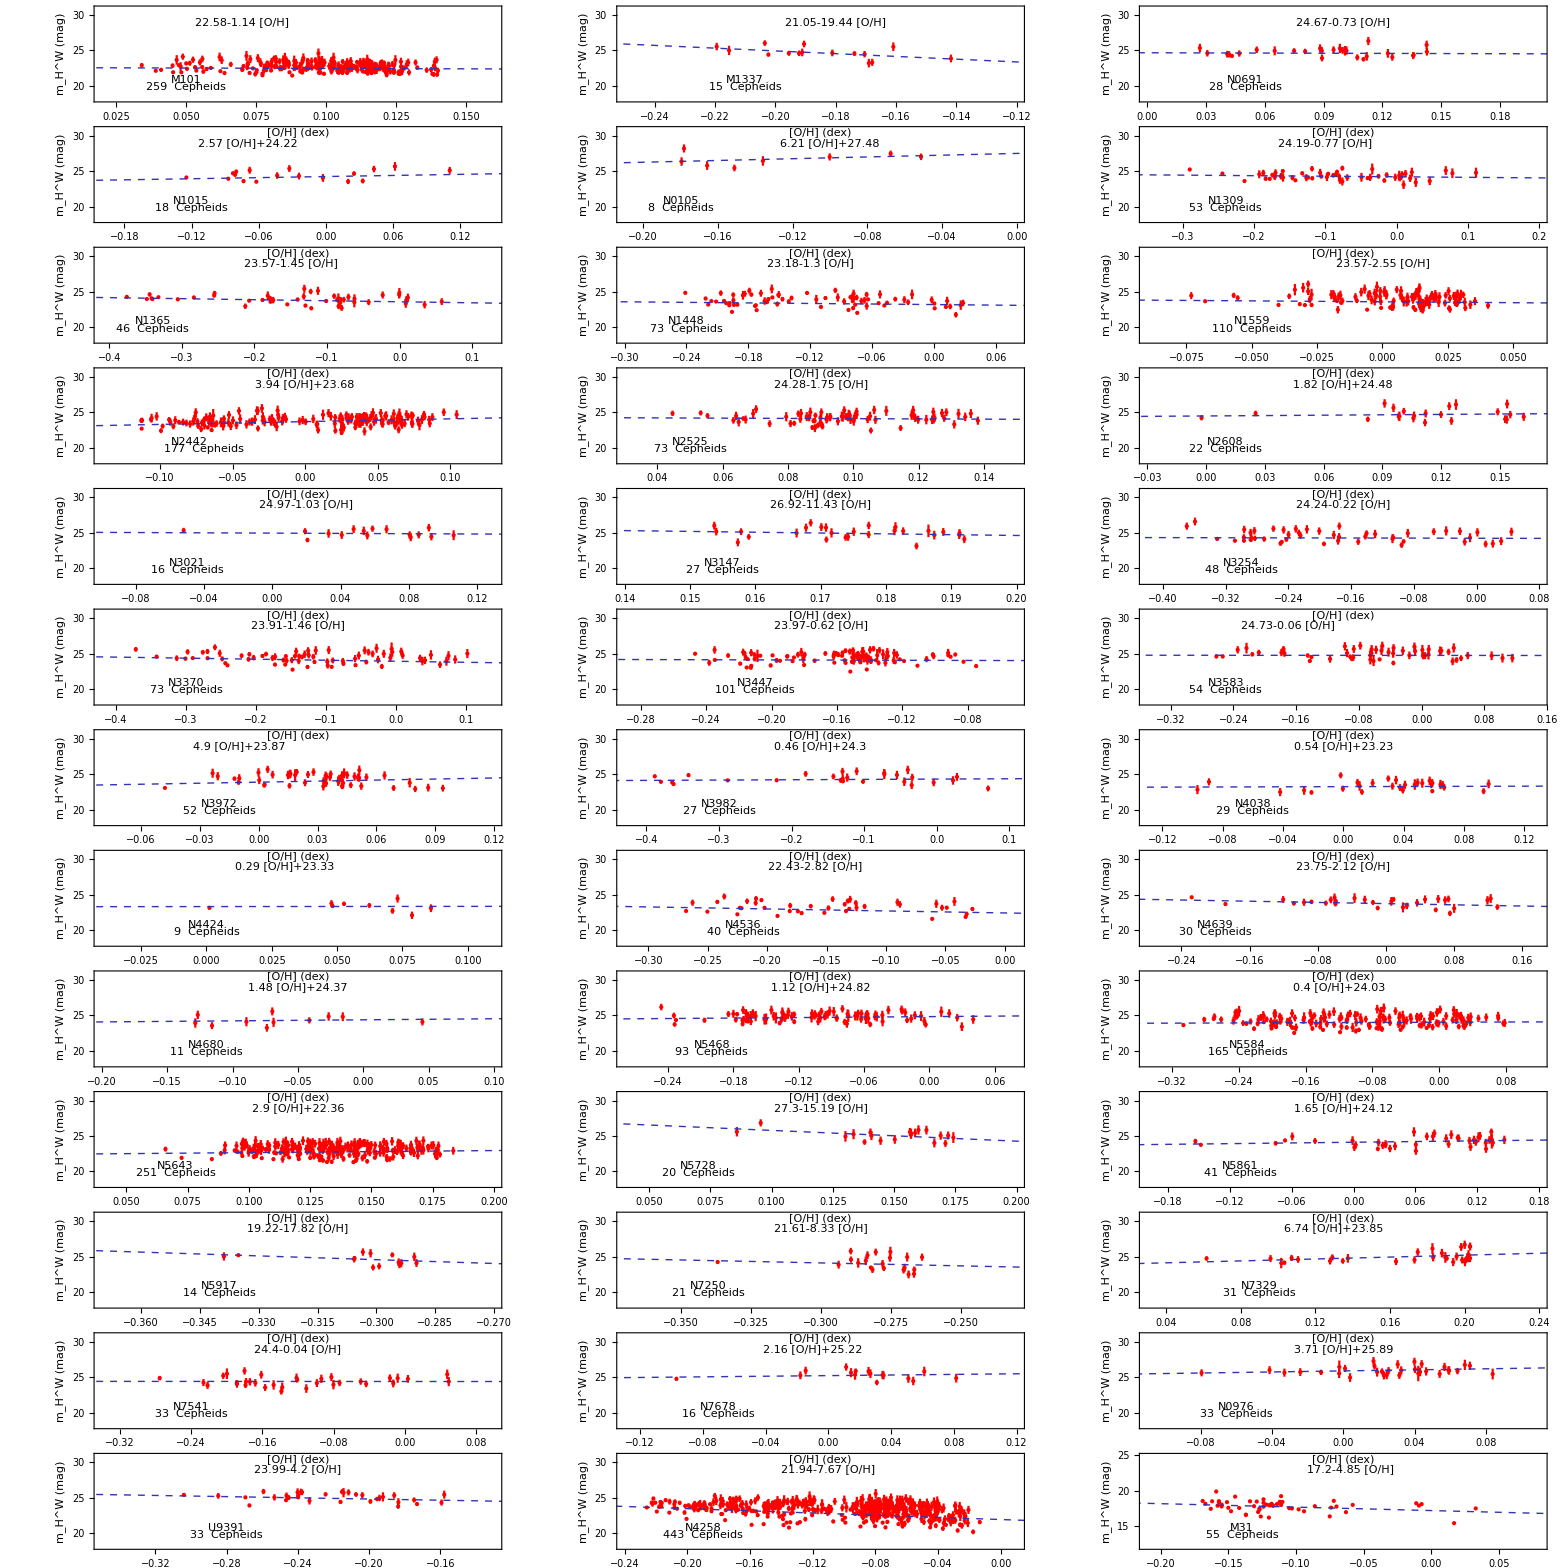

```mathematica
figzallnocov=GraphicsGrid[{{tabfigcsnocov[[1,2]],tabfigcsnocov[[2,2]],tabfigcsnocov[[3,2]]},{tabfigcsnocov[[4,2]],tabfigcsnocov[[5,2]],tabfigcsnocov[[6,2]]},{tabfigcsnocov[[7,2]],tabfigcsnocov[[8,2]],tabfigcsnocov[[9,2]]},{tabfigcsnocov[[10,2]],tabfigcsnocov[[11,2]],tabfigcsnocov[[12,2]]},{tabfigcsnocov[[13,2]],tabfigcsnocov[[14,2]],tabfigcsnocov[[15,2]]},{tabfigcsnocov[[16,2]],tabfigcsnocov[[17,2]],tabfigcsnocov[[18,2]]},{tabfigcsnocov[[19,2]],tabfigcsnocov[[20,2]],tabfigcsnocov[[21,2]]},{tabfigcsnocov[[22,2]],tabfigcsnocov[[23,2]],tabfigcsnocov[[24,2]]},{tabfigcsnocov[[25,2]],tabfigcsnocov[[26,2]],tabfigcsnocov[[27,2]]},{tabfigcsnocov[[28,2]],tabfigcsnocov[[29,2]],tabfigcsnocov[[30,2]]},{tabfigcsnocov[[31,2]],tabfigcsnocov[[32,2]],tabfigcsnocov[[33,2]]},{tabfigcsnocov[[34,2]],tabfigcsnocov[[35,2]],tabfigcsnocov[[36,2]]},{tabfigcsnocov[[37,2]],tabfigcsnocov[[38,2]],tabfigcsnocov[[39,2]]}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"figzallnocov.pdf",figzallnocov,ImageResolution->1000];
```

## Independently fitted slopes Z_W of the metallicity relations (ignored non-diagonal terms) - Figure 2

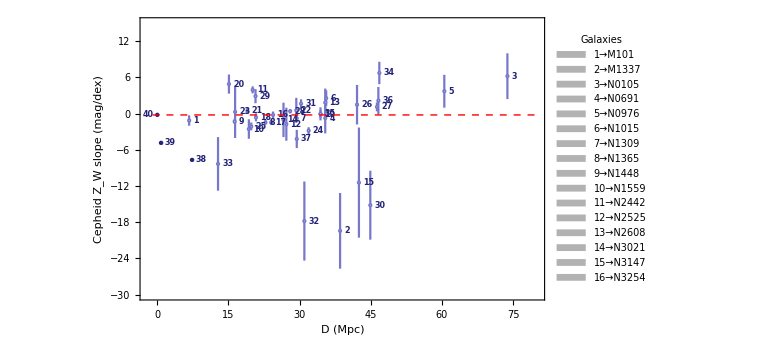

```mathematica
slopeernocov[galrank_,taballnocov_]:=Table[{galrank[[i,5]],taballnocov[[i,4]],taballnocov[[i,5]]},{i,1,39}]
slernocov=Join[slopeernocov[galrank,taballnocov],{{0,-0.20,0.12}}];
plslernocov=ErrorListPlot[slernocov,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{-1,80},{-30,25}},FrameLabel->{"D (Mpc)","Cepheid  Z_W slope (mag/dex)"},PlotStyle->{PointSize->Medium,Lighter[RGBColor[0.2,0.2,0.7]]},Epilog->{Dashed,Red,Line[{{-1,-0.217},{80,-0.217}}]},ImageSize->Large];
legendnocov=SwatchLegend[{RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7],RGBColor[0.2,0.2,0.7]},{galrank[[1,1]] ->galrank[[1,4]]  ,galrank[[2,1]] ->galrank[[2,4]] ,galrank[[5,1]] ->galrank[[5,4]] ,galrank[[3,1]] ->galrank[[3,4]] ,galrank[[36,1]] ->galrank[[36,4]],galrank[[4,1]] ->galrank[[4,4]] ,galrank[[6,1]] ->galrank[[6,4]] ,galrank[[7,1]] ->galrank[[7,4]] ,galrank[[8,1]] ->galrank[[8,4]] ,galrank[[9,1]] ->galrank[[9,4]],galrank[[10,1]] ->galrank[[10,4]],galrank[[11,1]] ->galrank[[11,4]],galrank[[12,1]] ->galrank[[12,4]],galrank[[13,1]] ->galrank[[13,4]],galrank[[14,1]] ->galrank[[14,4]],galrank[[15,1]] ->galrank[[15,4]],galrank[[16,1]] ->galrank[[16,4]]  ,galrank[[17,1]] ->galrank[[17,4]] ,galrank[[18,1]] ->galrank[[18,4]] ,galrank[[19,1]] ->galrank[[19,4]] ,galrank[[20,1]] ->galrank[[20,4]] ,galrank[[21,1]] ->galrank[[21,4]] ,galrank[[22,1]] ->galrank[[22,4]] ,galrank[[23,1]] ->galrank[[23,4]] ,galrank[[24,1]] ->galrank[[24,4]],galrank[[25,1]] ->galrank[[25,4]],galrank[[26,1]] ->galrank[[26,4]],galrank[[27,1]] ->galrank[[27,4]],galrank[[28,1]] ->galrank[[28,4]],galrank[[29,1]] ->galrank[[29,4]],galrank[[30,1]] ->galrank[[30,4]],galrank[[31,1]] ->galrank[[31,4]] ,galrank[[32,1]] ->galrank[[32,4]] ,galrank[[33,1]] ->galrank[[33,4]] ,galrank[[34,1]] ->galrank[[34,4]],galrank[[35,1]] ->galrank[[35,4]],galrank[[37,1]] ->galrank[[37,4]],38->N4258,39->M31,40->MW},LegendLayout->{"Column",2},LabelStyle->{Bold,Darker[RGBColor[0.2,0.2,0.7]],FontSize->9},LegendMarkers->Graphics[{Black,Opacity[0.3],Disk[]}],LegendLabel->"Galaxies",LegendMarkerSize->6,LegendFunction->(Framed[#,RoundingRadius->3,FrameStyle->White]&),LegendMargins->0.1];
plslerlabelnocov=ListPlot[Table[Labeled[{galrank[[i,5]],taballnocov[[i,4]]},galrank[[i,1]],Right],{i,1,37}],Axes->False, Frame->True,BaseStyle->FontSize->8,LabelStyle->Directive[Bold,FontFamily->"Helvetica",8,Darker[RGBColor[0.2,0.2,0.7]]],PlotRange->{{-1,80},{-30,25}},PlotStyle->{PointSize[0.00001],White},PlotLegends->legendnocov,ImageSize->Large];
lab2nocov=ListPlot[{Labeled[{0,-0.2},"40" ,Left],Labeled[{7.3,taballnocov[[38,4]]},"  38",Right],Labeled[{0.76,taballnocov[[39,4]]},"  39" ,Right]},
Frame->True,Axes->None,LabelStyle->Directive[Bold,FontFamily->"Helvetica",8,Darker[RGBColor[0.2,0.2,0.7]],Spacings->4],BaseStyle->FontSize->20,PlotRange->{{-2,40},{-30,25}},PlotStyle->{PointSize->Small,Darker[RGBColor[0.2,0.2,0.7]]}];
slopeer2nocov[galrank_,taballnocov_]:=Table[{galrank[[i,3]],taballnocov[[i,4]],taballnocov[[i,5]]},{i,4,39}]
sler2nocov=Join[slopeer2nocov[galrank,taballnocov],{{1,-0.20,0.12}}];
plsler2nocov=ErrorListPlot[sler2nocov,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{-1,44},{-30,15}},GridLines->{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42},None},FrameLabel->{"","Cepheid m_H^W slope Z_W (mag/dex)"},PlotStyle->{PointSize->Medium,Lighter[RGBColor[0.2,0.2,0.7]]},Epilog->{Dashed,Red,Line[{{-1,-0.217},{80,-0.217}}]},ImageSize->Large];
figz10nocov=Show[plsler2nocov,FrameStyle->Directive[Black,Thick],FrameTicks->{{{-28,-24,-20,-16,-12,-8,-4,0,4,8,12,16},None},{{{1,Rotate["MW",90 Degree]},{2,Rotate["LMC",90 Degree]},{3,Rotate["SMC",90 Degree]},{4,Rotate["N4258",90 Degree]},{5,Rotate["M31",90 Degree]},{6,Rotate["N5643",90 Degree]},{7,Rotate["N1448",90 Degree]},{8,Rotate["M101",90 Degree]},{9,Rotate["N3447",90 Degree]},{10,Rotate["N5584",90 Degree]},{11,Rotate["N1559",90 Degree]},{12,Rotate["N4536",90 Degree]},{13,Rotate["N2442",90 Degree]},{14,Rotate["N3370",90 Degree]},{15,Rotate["N3583",90 Degree]},{16,Rotate["N3254",90 Degree]},{17,Rotate["N3972",90 Degree]},{18,Rotate["N5468",90 Degree]},{19,Rotate["N3982",90 Degree]},{20,Rotate["N1365",90 Degree]},{21,Rotate["N2525",90 Degree]},{22,Rotate["N7250",90 Degree]},{23,Rotate["U9391",90 Degree]},{24,Rotate["N1015",90 Degree]},{25,Rotate["N1309",90 Degree]},{26,Rotate["N5861",90 Degree]},{27,Rotate["N4639",90 Degree]},{28,Rotate["N0691",90 Degree]},{29,Rotate["N4038",90 Degree]},{30,Rotate["N7541",90 Degree]},{31,Rotate["N2608",90 Degree]},{32,Rotate["N3147",90 Degree]},{33,Rotate["N7329",90 Degree]},{34,Rotate["M1337",90 Degree]},{35,Rotate["N3021",90 Degree]},{36,Rotate["N7678",90 Degree]},{37,Rotate["N5917",90 Degree]},{38,Rotate["N4680",90 Degree]},{39,Rotate["N0976",90 Degree]},{40,Rotate["N4424",90 Degree]},{41,Rotate["N5728",90 Degree]},{42,Rotate["N0105",90 Degree]}},None}},PlotRange->{{-0.1,43},{-30,15.}},FrameTicksStyle->Directive[Thick,Black,FontFamily->"Helvetica",12], Frame->True,ImageSize->Large];
figz10dnocov=Show[plslernocov,plslerlabelnocov,lab2nocov,FrameStyle->Directive[Black,Thick,FontFamily->"Times",20],PlotRange->{{-2,80},{-30,15.}},Frame->True,ImageSize->Large]
Export[NotebookDirectory[]<>"figz10dnocov.pdf",figz10dnocov,ImageResolution->1000];
```

## Homogeneity of the Cepheid modeling parameter Z_W - Binned Cepheid slopes Z_W for the high distance bin (D>Dc) and the low distance bin (D<Dc) - Figure 4

```mathematica
chi2nocov [z_?NumberQ]:=Sum[((slernocov[[i,2]]-z)/Sqrt[slernocov[[i,3]]^2+0^2])^2,{i,1,40}];(* see Eq.28 (Subscript[σ, scat]=0) *)
chi2minnocov=FindMinimum[chi2nocov [z],{z,0}]
```

{858.642,{z→-1.03327}}

```mathematica
chired=chi2minnocov[[1]]/39
```

22.0165

```mathematica
chi2nocov [z_?NumberQ]:=Sum[((slernocov[[i,2]]-z)/Sqrt[slernocov[[i,3]]^2+3.2^2])^2,{i,1,40}];(* see Eq.29 (Subscript[σ, scat]=3.2) *)
chi2minnocov=FindMinimum[chi2nocov [z],{z,0}]
```

{45.1532,{z→-0.577048}}

```mathematica
chired=chi2minnocov[[1]]/39
```

1.15777

```mathematica
tabdssdnocov={};
tabbfwnocov ={};
tabbfwsnocov={};
tabbfwlnocov ={};
tabchired={};
Do[
slersnocov=Select[slernocov,#[[1]]<dspltnocov &];

slerlnocov=Select[slernocov,#[[1]]>dspltnocov &];

If[dspltnocov<10,chi2snocov [zs1_?NumberQ]:=Sum[((slersnocov[[i,2]]-zs1)/Sqrt[slersnocov[[i,3]]^2+2.2^2])^2,{i,1,Length[slersnocov]}],chi2snocov [zs2_?NumberQ]:=Sum[((slersnocov[[i,2]]-zs2)/Sqrt[slersnocov[[i,3]]^2+2.8^2])^2,{i,1,Length[slersnocov]}]];
chi2sminnocov=FindMinimum[chi2snocov [z],{z,0}];
wminsnocov =chi2sminnocov [[2,1,2]];
chi2smincnocov =chi2sminnocov [[1]];
s11snocov =FindRoot[chi2snocov [z]==chi2sminnocov [[1]]+1,{z,chi2sminnocov [[2,1,2]]+0.5}][[1,2]]-chi2sminnocov [[2,1,2]];
If[44<dspltnocov<47,chi2lnocov [zl1_?NumberQ]:=Sum[((slerlnocov[[i,2]]-zl1)/Sqrt[slerlnocov[[i,3]]^2+1.2^2])^2,{i,1,Length[slerlnocov]}],If[28<dspltnocov<45,chi2lnocov [zl1_?NumberQ]:=Sum[((slerlnocov[[i,2]]-zl1)/Sqrt[slerlnocov[[i,3]]^2+5^2])^2,{i,1,Length[slerlnocov]}],If[dspltnocov>46,chi2lnocov [zl2_?NumberQ]:=Sum[((slerlnocov[[i,2]]-zl2)/Sqrt[slerlnocov[[i,3]]^2+0.^2])^2,{i,1,Length[slerlnocov]}],chi2lnocov [zl3_?NumberQ]:=Sum[((slerlnocov[[i,2]]-zl3)/Sqrt[slerlnocov[[i,3]]^2+3.2^2])^2,{i,1,Length[slerlnocov]}]]]];
chi2lminnocov =FindMinimum[chi2lnocov [z],{z,0}];
wminlnocov =chi2lminnocov [[2,1,2]];
chi2lmincnocov =chi2lminnocov [[1]];
s11lnocov =FindRoot[chi2lnocov [z]==chi2lminnocov [[1]]+1,{z,chi2lminnocov [[2,1,2]]+0.5}][[1,2]]-chi2lminnocov [[2,1,2]];

sdistminnocov =Abs[(wminlnocov -wminsnocov)]/(s11lnocov ^2+s11snocov ^2)^0.5;
AppendTo[tabchired,{dspltnocov,chi2sminnocov[[1]]/ Length[slersnocov],chi2lminnocov [[1]]/Length[slerlnocov]}];
AppendTo[tabbfwnocov,{dspltnocov,wminsnocov ,wminlnocov }];
AppendTo[tabbfwsnocov ,{dspltnocov,wminsnocov ,s11snocov }];
AppendTo[tabbfwlnocov ,{dspltnocov,wminlnocov ,s11lnocov }];
AppendTo[tabdssdnocov ,{dspltnocov,sdistminnocov }],{dspltnocov,1,60,1}]
```

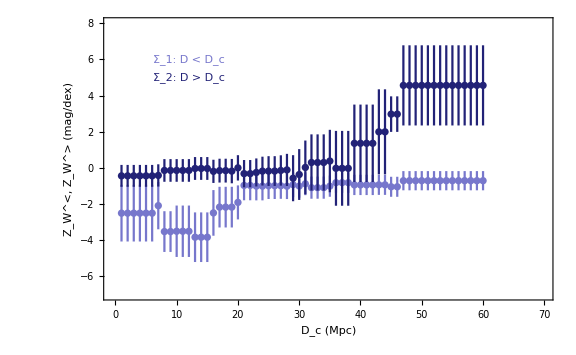

```mathematica
figwslinnocov=ErrorListPlot[{tabbfwsnocov,tabbfwlnocov},Axes->False,Frame->True,FrameLabel->{"D_c [Mpc]","Ζ_W^<, Ζ_W^> (mag/dex)"},BaseStyle->{Medium,GrayLevel[.3],FontFamily->"Times",8},LabelStyle->Directive[GrayLevel[.3],Small],PlotRange->{{-0.5,37},{-4,4}},PlotStyle->{Lighter[RGBColor[0.2,0.2,0.7]],Darker[RGBColor[0.2,0.2,0.7]]},FrameStyle -> Directive[GrayLevel[.3], Thick],ImageSize->250];
figwslnocovz=ErrorListPlot[{tabbfwsnocov,tabbfwlnocov},Axes->False,Frame->True,FrameLabel->{"D_c (Mpc)","Ζ_W^<, Ζ_W^>  (mag/dex)"},BaseStyle->{Large,FontFamily->"Times",20},LabelStyle->Directive[Black,Large],PlotRange->{{-0.5,70},{-7,8}},PlotStyle->{Lighter[RGBColor[0.2,0.2,0.7]],Darker[RGBColor[0.2,0.2,0.7]]},ImageSize->Large, FrameStyle -> Directive[Black, Thick],Epilog->{{Lighter[RGBColor[0.2,0.2,0.7]],Inset["Σ_1: D < D_c",{12,6}]},{Darker[RGBColor[0.2,0.2,0.7]],Inset["Σ_2: D > D_c",{12,5}]}}]
```

```mathematica
Export[NotebookDirectory[]<>"figwslnocovz.pdf",figwslnocovz,ImageResolution->1000];
```

## σ-distance between the best fit high bin and low bin slopes Z_W- Figure 5

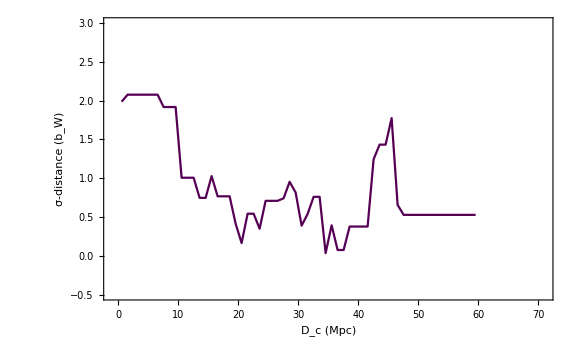
```mathematica
figwsdnocovz=ListPlot[tabdssdnocov,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance (Z_W)"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-0.5,5}},Axes->False,PlotStyle->{Lighter[RGBColor[0.2,0.2,0.7]]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]];
figwsdnocovb=-Graphics-;
figsdistnocovzb=Show[figwsdnocovb,figwsdnocovz,Graphics[{Inset[" - Independently-fitted slopes Z_W ",{19,3.9},BaseStyle->{Italic,Bold,Lighter[RGBColor[0.2,0.2,0.7]],FontFamily->"Times",12}]}],Graphics[{Inset[" - Independently-fitted slopes b_W ",{19,3.5},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],
Graphics[{Inset[" σ-distance=(s_>)/(√(σ_>^2)) ,  with s: slope",{54,3.9},BaseStyle->{Italic,Bold,Darker[Gray],FontFamily->"Times",12}]}],FrameLabel->{"D_c (Mpc)","σ-distance"},PlotRange->{{-0.01,73},{-0.5,4.5}},ImageSize->Large]
```

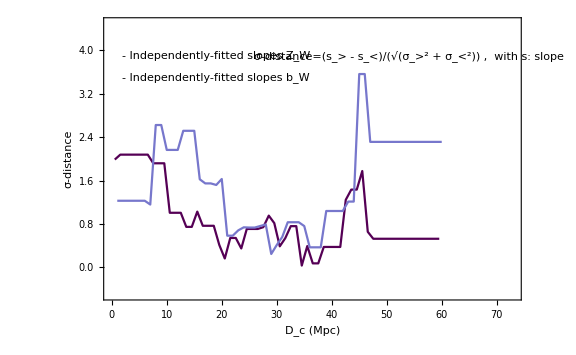

```mathematica
Export[NotebookDirectory[]<>"figsdistnocovzb2.pdf",figsdistnocovzb,ImageResolution->1000];
```

## Results - Table C1

```mathematica
tablebw={{"M101",6.71,-2.9885525198046707,0.13757745274833924},{"M1337",38.53,-3.9975102887178764,0.8473048369794082},{"N0691",35.4,-2.6384519706473384,0.5703122675505086},{"N1015",35.6,-3.6291648225444533,0.4322710009537037},{"N0105",73.8,-5.131782027812733,2.1286478364532235},{"N1309",29.4,-3.2338387597569636,0.43650236965288886},{"N1365",22.8,-2.9038705025509444,0.3658918320273874},{"N1448",16.3,-3.2056795430991087,0.12213537109875847},{"N1559",19.3,-3.265728537160385,0.17987799618617495},{"N2442",20.1,-3.048674356103883,0.2036077538093411},{"N2525",27.2,-3.199525401296569,0.37138654734331616},{"N2608",35.4,-3.242702363761282,0.7257536553919927},{"N3021",26.6,-3.2958395259840927,0.8867280447948027},{"N3147",42.5,-4.7223762761577746,0.7271071129741669},{"N3254",24.4,-3.051122027433621,0.31077329498537326},{"N3370",24,-3.545684161579402,0.23208263165395784},{"N3447",20.8,-3.4813163802495004,0.13467058028532705},{"N3583",34.4,-2.5686048243437654,0.30759601491443556},{"N3972",15.1,-3.57674432105523,0.3176453238462781},{"N3982",19,-2.470886130500503,0.3610603007967995},{"N4038",29.3,-2.625194467833353,0.4670281710644978},{"N4424",16.4,1.0133836120207889,1.261328730037476},{"N4536",31.9,-3.25200921106034,0.19315431319638313},{"N4639",19.8,-3.0848312803595945,0.5130496164824688},{"N4680",42.1,-3.121854737987178,1.2212861953696066},{"N5468",46.3,-2.6216095447862244,0.3451243977530232},{"N5584",28,-3.2645745721564565,0.16074455893507675},{"N5643",20.7,-3.0970726924889505,0.12448260447561688},{"N5728",44.9,-5.090139557579278,1.3413145233442292},{"N5861",30.3,-2.503147147398977,0.45004991040405135},{"N5917",31,-4.536766516563148,1.1663167810150112},{"N7250",12.8,-2.7489997837567444,0.38557921960987485},{"N7329",46.8,-3.035435834441614,0.7623538808909367},{"N7541",34.4,-3.5419313782535937,0.7066617382934156},{"N7678",46.6,-2.728618676187125,1.026777389875957},{"N0976",60.5,-1.7946790021815104,1.2377844004226584},{"U9391",29.4,-3.3343989374152443,0.426255884235561},{"N4258",7.4,-3.324130977276866,0.055668029725503276},{"M31",0.86,-3.2893528077376004,0.07453772727993539},{MW,0,-3.26192,0.051433}};
slopeernocovname[galrank_,taballnocov_]:=Table[{galrank[[i,4]],galrank[[i,5]],Round[tablebw[[i,3]],0.01],Round[tablebw[[i,4]],0.01],0.18,Round[taballnocov[[i,4]],0.01],Round[taballnocov[[i,5]],0.01],3.2},{i,1,39}];
slernocovname=Join[slopeernocovname[galrank,taballnocov],{{MW,0,-3.26,0.05,0.18,-0.20,0.12,3.2}}];
MatrixForm[slernocovname]
```

(M101 | 6.71 | -2.99 | 0.14 | 0.18 | -1.14 | 0.86 | 3.2
M1337 | 38.53 | -4. | 0.85 | 0.18 | -19.44 | 6.27 | 3.2
N0691 | 35.4 | -2.64 | 0.57 | 0.18 | -0.73 | 2.54 | 3.2
N1015 | 35.6 | -3.63 | 0.43 | 0.18 | 2.57 | 1.3 | 3.2
N0105 | 73.8 | -5.13 | 2.13 | 0.18 | 6.21 | 3.8 | 3.2
N1309 | 29.4 | -3.23 | 0.44 | 0.18 | -0.77 | 0.59 | 3.2
N1365 | 22.8 | -2.9 | 0.37 | 0.18 | -1.45 | 0.39 | 3.2
N1448 | 16.3 | -3.21 | 0.12 | 0.18 | -1.3 | 0.39 | 3.2
N1559 | 19.3 | -3.27 | 0.18 | 0.18 | -2.55 | 1.62 | 3.2
N2442 | 20.1 | -3.05 | 0.2 | 0.18 | 3.94 | 0.58 | 3.2
N2525 | 27.2 | -3.2 | 0.37 | 0.18 | -1.75 | 2.74 | 3.2
N2608 | 35.4 | -3.24 | 0.73 | 0.18 | 1.82 | 2.33 | 3.2
N3021 | 26.6 | -3.3 | 0.89 | 0.18 | -1.03 | 2.85 | 3.2
N3147 | 42.5 | -4.72 | 0.73 | 0.18 | -11.43 | 9.13 | 3.2
N3254 | 24.4 | -3.05 | 0.31 | 0.18 | -0.22 | 0.57 | 3.2
N3370 | 24 | -3.55 | 0.23 | 0.18 | -1.46 | 0.4 | 3.2
N3447 | 20.8 | -3.48 | 0.13 | 0.18 | -0.62 | 0.66 | 3.2
N3583 | 34.4 | -2.57 | 0.31 | 0.18 | -0.06 | 0.62 | 3.2
N3972 | 15.1 | -3.58 | 0.32 | 0.18 | 4.9 | 1.58 | 3.2
N3982 | 19 | -2.47 | 0.36 | 0.18 | 0.46 | 0.47 | 3.2
N4038 | 29.3 | -2.63 | 0.47 | 0.18 | 0.54 | 2.07 | 3.2
N4424 | 16.4 | 1.01 | 1.26 | 0.18 | 0.29 | 4.33 | 3.2
N4536 | 31.9 | -3.25 | 0.19 | 0.18 | -2.82 | 0.56 | 3.2
N4639 | 19.8 | -3.08 | 0.51 | 0.18 | -2.12 | 0.64 | 3.2
N4680 | 42.1 | -3.12 | 1.22 | 0.18 | 1.48 | 3.27 | 3.2
N5468 | 46.3 | -2.62 | 0.35 | 0.18 | 1.12 | 0.74 | 3.2
N5584 | 28 | -3.26 | 0.16 | 0.18 | 0.4 | 0.36 | 3.2
N5643 | 20.7 | -3.1 | 0.12 | 0.18 | 2.9 | 1.17 | 3.2
N5728 | 44.9 | -5.09 | 1.34 | 0.18 | -15.19 | 5.71 | 3.2
N5861 | 30.3 | -2.5 | 0.45 | 0.18 | 1.65 | 0.72 | 3.2
N5917 | 31 | -4.54 | 1.17 | 0.18 | -17.82 | 6.56 | 3.2
N7250 | 12.8 | -2.75 | 0.39 | 0.18 | -8.33 | 4.44 | 3.2
N7329 | 46.8 | -3.04 | 0.76 | 0.18 | 6.74 | 1.86 | 3.2
N7541 | 34.4 | -3.54 | 0.71 | 0.18 | -0.04 | 1.08 | 3.2
N7678 | 46.6 | -2.73 | 1.03 | 0.18 | 2.16 | 2.27 | 3.2
N0976 | 60.5 | -1.79 | 1.24 | 0.18 | 3.71 | 2.73 | 3.2
U9391 | 29.4 | -3.33 | 0.43 | 0.18 | -4.2 | 1.51 | 3.2
N4258 | 7.4 | -3.32 | 0.06 | 0.18 | -7.67 | 0.31 | 3.2
M31 | 0.86 | -3.29 | 0.07 | 0.18 | -4.85 | 0.35 | 3.2
MW | 0 | -3.26 | 0.05 | 0.18 | -0.2 | 0.12 | 3.2)